```mathematica
SymbolToKey[s_]:=FromDigits[StringDrop[SymbolName[s],1]]
```

```mathematica
RelationsToEdges[key_,assoc_]:=Block[{current=assoc[key],rel2, result={}, lhs, rhs,one,two,three},
Table[
rel2=Simplify[rel];
lhs=rel2[[1]];
rhs=rel2[[2]];
If[Length[lhs]==0,
one=SymbolToKey[lhs];
two=SymbolToKey[rhs[[1]]];
three=SymbolToKey[rhs[[2]]];
,
one=SymbolToKey[rhs];
two=SymbolToKey[lhs[[1]]];
three=SymbolToKey[lhs[[2]]]
];
If[one==1&&(two==0||three==0),Print[{key,rel}]];
(*If[ToString[stubbornForm5[one]["comp"]]!=ToString[stubbornForm5[two]["comp"]],
result=Append[result,{one->two}];
];
If[ToString[stubbornForm5[one]["comp"]]!=ToString[stubbornForm5[three]["comp"]],
result=Append[result,{one->three}];
];*)
result=Append[result,{one->two,one->three}];
,{rel,current["relations"]}
];
Flatten[result]
]
```

```mathematica
allDependencies5=DeleteDuplicates[ Flatten[Table[RelationsToEdges[key,stubbornForm5],{key,Keys[stubbornForm5]}]]];Take[allDependencies5,5]
```

{0→19683,0→39366,0→13122,0→6561,0→2187}

```mathematica
Length[allDependencies]
```

14710

```mathematica
g5=Graph[allDependencies5];
```

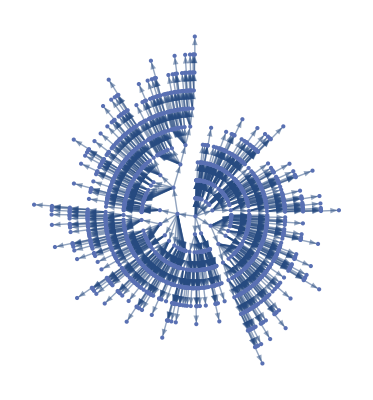

```mathematica
span5=FindSpanningTree[ g5,GraphLayout->"RadialEmbedding"]
```

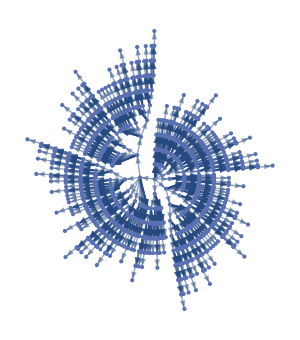

```mathematica
depGraph=Graph[span5,  GraphLayout->"RadialEmbedding",
  ImageSize->300,EdgeStyle->Arrowheads[0.001]]
```

```mathematica
allDependencies4=DeleteDuplicates[ Flatten[Table[RelationsToEdges[key,stubbornForm4],{key,Keys[stubbornForm4]}]]];Take[allDependencies4,5]
```

{0→243,0→486,0→162,0→81,0→27}

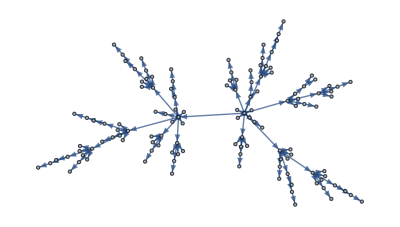

```mathematica
span4=FindSpanningTree[ {Graph[allDependencies4//Sort],0}]
```

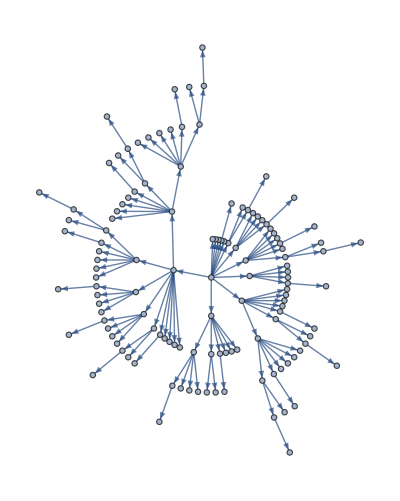

```mathematica
depGraph=Graph[span4,  GraphLayout->"RadialEmbedding",  ImageSize->400]
```